```mathematica
ClearAll["Global`*"]
```

```mathematica
Taylor[f_,t_,x0__,t0_,k_]:=(d=Length[x0];
g[x_]:=x0+f[x0]*(x-t0);h=Array[hh,d];
For[j=2,j<=k,j++,For[i=1,i<=d,i++,h[[i]][z_]=g[x][[i]]+(z-t0)ˆj/j!*D[f[g[s]][[i]],{s,j-1}]/. {s->t0};];v={};
For[i=1,i<=d,i++,v=Append[v,h[[i]][x]]];g[x_]=v];
Return[g[t]])
f[x__]:={f1[x[[1]],x[[2]]],f2[x[[1]],x[[2]]]}
Taylor[f,t,{x1,x2},0,2]
```

{x1+t f1[x1,x2]+1/2 ˆj t (f2[x1,x2] f1^(0,1)[x1,x2]+f1[x1,x2] f1^(1,0)[x1,x2]),x2+t f2[x1,x2]+1/2 ˆj t (f2[x1,x2] f2^(0,1)[x1,x2]+f1[x1,x2] f2^(1,0)[x1,x2])}

```mathematica
ClearAll["Global`*"]
```

```mathematica
B[f_,t_,x0_,t0_,n_]:=(If[n==0,Return[x0],If[n==1,Return[x0+(t-t0)*f[x0]],sample=x0+(t-t0)*f[x0];g=Graph[{1->2}];
g=Graph[g,VertexLabels->{1->D[f[y],y]}];
g=Graph[g,VertexLabels->{2->f[y]}];m=1;
sample=sample+1/2*(t-t0)ˆVertexCount[g]*Product[ff[[2]],{ff,List@@@PropertyValue[g,VertexLabels]}]/. {y->x0};
list={g};
While[m<=(n-2),temp=list;list={};
Do[l=VertexCount[g];
For[j=1,j<=l,j++,gg=VertexAdd[g,{l+1}];
gg=Graph[gg,VertexLabels->{l+1->f[y]}];
lab=Sort[List@@@PropertyValue[gg,VertexLabels]][[j]][[2]];
gg=Graph[gg,VertexLabels->{j->D[lab,y]}];
gg=EdgeAdd[gg,j->l+1];Print[gg];
sample=sample+(t-t0)ˆ(l+1)/(l+1)!*Product[ff[[2]],{ff,List@@@PropertyValue[gg,VertexLabels]}]/. {y->x0};
list=Append[list,gg]],{g,temp}];m=m+1];
Return[sample]]]);
```

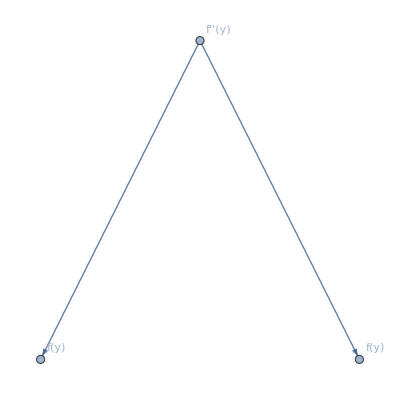

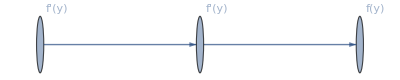

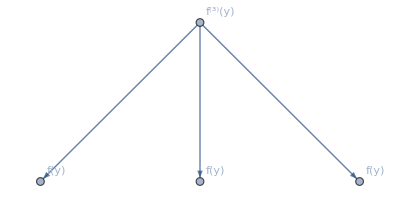

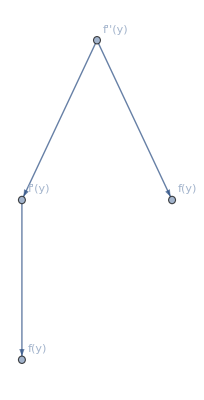

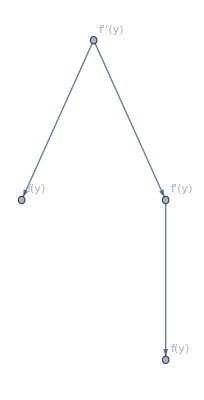

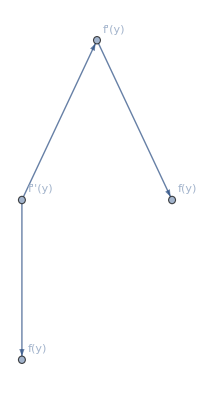

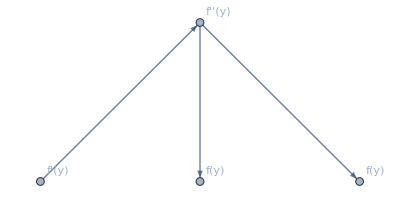

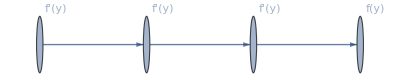

x0+(t-t0) f[x0]+1/2 (t-t0) f[x0] ˆVertexCount[-Graphics-] f'[x0]+1/2 ˆ (t-t0) f[x0] f'[x0]^2+1/6 ˆ (t-t0) f[x0] f'[x0]^3+1/2 ˆ (t-t0) f[x0]^2 f''[x0]+2/3 ˆ (t-t0) f[x0]^2 f'[x0] f''[x0]+1/6 ˆ (t-t0) f[x0]^3 f^(3)[x0]

```mathematica
B[f,t,x0,t0,4]
```

```mathematica
MCsample[f_,t_,x0_,dist_]:=(n=RandomVariate[dist];
If[n==0,Return[x0/PDF[dist,0]],If[n==1,Return[t*f[x0]/PDF[dist,1]],g=Graph[{1->2}];
g=Graph[g,VertexLabels->{1->D[f[y],y]}];
g=Graph[g,VertexLabels->{2->f[y]}];m=1;
While[m<=(n-2),l=VertexCount[g];
j=RandomVariate[DiscreteUniformDistribution[{1,l}]];
g=VertexAdd[g,{l+1}];
g=Graph[g,VertexLabels->{l+1->f[y]}];
lab=Sort[List@@@PropertyValue[g,VertexLabels]][[j]][[2]];
g=Graph[g,VertexLabels->{j->D[lab,y]}];
g=EdgeAdd[g,j->l+1];m++];
sample=Product[ff[[2]],{ff,List@@@PropertyValue[g,VertexLabels]}]/. {y->x0};
Return[sample*tˆn/PDF[dist,n]/n]]]);
f[y_]:=Exp[y]
MCsample[f,t,x0,GeometricDistribution[0.5]]
```

8. ⅇ^(4 x0) tˆn

```mathematica
B[f_,t_,x0__,t0_,n_]:=(d=Length[x0];
If[n==0,Return[{x0,1}],If[n==1,Return[{x0+(t-t0)*f[x0],2}],count=2;
sample=x0+(t-t0)*f[x0];
g=ConstantArray[Graph[{1->2}],d];ii=Array[i,n];
For[ii[[1]]=1,ii[[1]]<=d,ii[[1]]++,g[[ii[[1]]]]=Graph[g[[ii[[1]]]],VertexLabels->{1->D[f[yy],yy[[ii[[1]]]]]}];
g[[ii[[1]]]]=Graph[g[[ii[[1]]]],VertexLabels->{2->f[yy][[ii[[1]]]]}];
m=1;count+=1;
sample+=1/2*(t-t0)ˆVertexCount[g[[ii[[1]]]]]*Product[ff[[2]],{ff,List@@@PropertyValue[g[[ii[[1]]]],VertexLabels]}]/. {yy->x0}];list=g;
While[m<=(n-2),temp=list;list={};
Do[l=VertexCount[g];
For[j=1,j<=l,j++,gg=VertexAdd[g,{l+1}];
lab=Sort[List@@@PropertyValue[gg,VertexLabels]][[j]][[2]];For[ii[[l]]=1,ii[[l]]<=d,ii[[l]]++,gg=Graph[gg,VertexLabels->{l+1->f[yy][[ii[[l]]]]}];
gg=Graph[gg,VertexLabels->{j->D[lab,yy[[ii[[l]]]]]}];
gg=EdgeAdd[gg,j->l+1];
GraphPlot[gg,PlotStyle->{FontSize->20,FontColor->Red}];
count+=1;
sample+=(t-t0)ˆ(l+1)/(l+1)!*Product[ff[[2]],{ff,List@@@PropertyValue[gg,VertexLabels]}]/. {yy->x0};list=Append[list,gg]]],{g,temp}];m++];
Return[{sample,count}]]]);
```

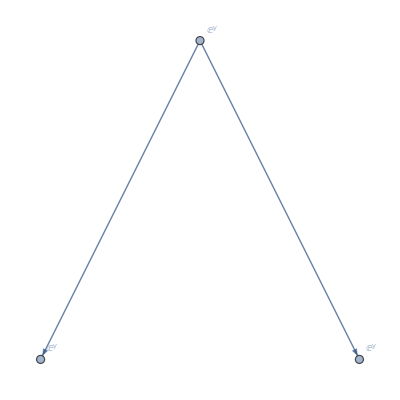

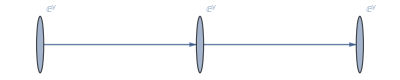

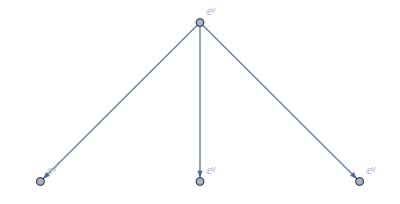

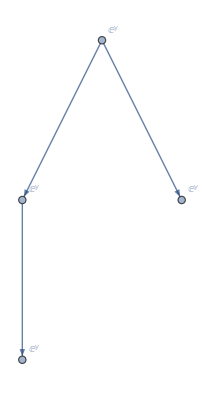

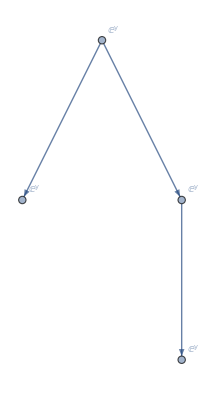

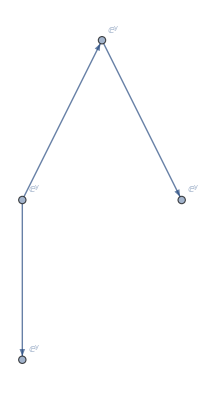

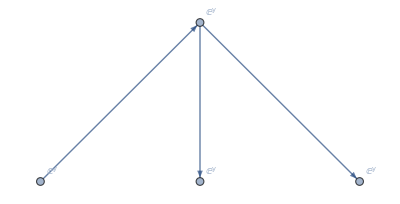

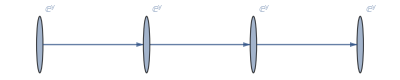

{{{{{{{{{{t+2 ˆ t+(t ˆVertexCount[-Graphics-])/2,t+3.06484 ˆ t+(t ˆVertexCount[-Graphics-])/2},{t+3.06484 ˆ t+(t ˆVertexCount[-Graphics-])/2,t+4.12969 ˆ t+(t ˆVertexCount[-Graphics-])/2}},{{t+3.06484 ˆ t+(t ˆVertexCount[-Graphics-])/2,t+4.12969 ˆ t+(t 1)/2},{t+1+1/2,1}}},{1}},{1}},{1}},{1}},1},1},1}
 |  |  |  |

```mathematica
x0={0,0.5};t0=0;t1=1.3885;
f[y__]:={1,y[[1]]*y[[2]]+y[[2]]ˆ2}
B[f,t,x0,t0,4]
```

```mathematica
MCsample[f_,t_,x0_,t0_,dist_]:=(n=RandomVariate[dist];
If[n==0,Return[x0/PDF[dist,0]],If[n==1,Return[(t-t0)*f[x0]/PDF[dist,1]],g=ConstantArray[Graph[{1->2}],d];ii=Array[i,n];
sample=0;
For[ii[[1]]=1,ii[[1]]<=d,ii[[1]]++,g[[ii[[1]]]]=Graph[g[[ii[[1]]]],VertexLabels->{1->D[f[yy],yy[[ii[[1]]]]]}];
g[[ii[[1]]]]=Graph[g[[ii[[1]]]],VertexLabels->{2->f[yy][[ii[[1]]]]}];
sample+=(t-t0)ˆ2/PDF[dist,2]/2*Product[ff[[2]],{ff,List@@@PropertyValue[g[[ii[[1]]]],VertexLabels]}]/. {yy->x0}];If[n==2,Return[sample]];sample=0;list=g;
m=1;While[m<=(n-2),temp=list;list={};
Do[l=VertexCount[g];
j=RandomVariate[DiscreteUniformDistribution[{1,l}]];
gg=VertexAdd[g,{l+1}];
lab=Sort[List@@@PropertyValue[gg,VertexLabels]][[j]][[2]];
For[ii[[l]]=1,ii[[l]]<=d,ii[[l]]++,gg=Graph[gg,VertexLabels->{l+1->f[yy][[ii[[l]]]]}];
gg=Graph[gg,VertexLabels->{j->D[lab,yy[[ii[[l]]]]]}];
gg=EdgeAdd[gg,j->l+1];
GraphPlot[gg,PlotStyle->{FontSize->20,FontColor->Red}];
If[m==(n-2),sample+=Product[ff[[2]],{ff,List@@@PropertyValue[gg,VertexLabels]}]/. {yy->x0}];list=Append[list,gg]],{g,temp}];m++];
Return[sample*(t-t0)ˆn/PDF[dist,n]/n]]]);
```

```mathematica
x0={0,0.5};t0=0;t1=1.3885;
f[y__]:={1,y[[1]]*y[[2]]+y[[2]]ˆ2}
MCsample[f,t,x0,t0,GeometricDistribution[0.5]]
```

{4. t,6.59489 t}